## Settings

```mathematica
imgsize=700;
```

```mathematica
eqn = D[D[f[x],x],x]-( a k Cot[k x]+i(omegam - a Sin[k x]Cos[2thetam]) a Sin[k x] )D[f[x],x]+(Sin[2 thetam]/2)^2 a^2 Sin[k x]^2 f[x]==0
```

1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0

```mathematica
DSolve[eqn,f[x],x]
```

DSolve[1/4 a^2 f[x] Sin[2 thetam]^2 Sin[k x]^2-(a k Cot[k x]+a i Sin[k x] (omegam-a Cos[2 thetam] Sin[k x])) f'[x]+f''[x]==0,f[x],x]

```mathematica
DSolve[f[x]+x D[f[x],x]==omegam/2-deltalambda[x]Sin[2thetam]/2,f[x],x]
```

{{f[x]→C[1]/x+(∫_1^x 1/2 (omegam-deltalambda[K[1]] Sin[2 thetam])ⅆK[1])/x}}

```mathematica
sys=I D[{phi1[x],phi2[x]},x]=={{0,(g0R+I g0I) Exp[I(-omegam+n0 k)x]},{(g0R-I g0I) Exp[-I(-omegam+n0 k)x],0}}.{phi1[x],phi2[x]}
```

{ⅈ phi1'[x],ⅈ phi2'[x]}=={ⅇ^(ⅈ (k n0-omegam) x) (ⅈ g0I+g0R) phi2[x],ⅇ^(-ⅈ (k n0-omegam) x) (-ⅈ g0I+g0R) phi1[x]}

```mathematica
DSolve[sys,{phi1,phi2},x]
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

```mathematica
%//FullSimplify
```

{{phi1→Function[{x},ⅇ^(1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) C[1]+ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x) C[2]],phi2→Function[{x},1/(2 (g0I-ⅈ g0R))ⅈ ⅇ^(-ⅈ (k n0-omegam) x+1/2 ⅈ (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) x) (k n0+ⅈ √(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)-omegam) C[1]+1/(2 (g0I-ⅈ g0R))ⅇ^(1/2 (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) x-ⅈ (k n0-omegam) x) (√(-4 (g0I^2+g0R^2)-(k n0-omegam)^2)+ⅈ (k n0-omegam)) C[2]]}}

## Understand The Hamiltonian

```mathematica
ClearAll[k,x,phi,function1,constant1]
DSolve[I D[function1[x],x]==constant1 Sin[k x+phi]function1[x],function1,x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-ⅈ constant1 (-(Cos[phi] Cos[k x])/k+(Sin[phi] Sin[k x])/k)) C[1]]}}

```mathematica
ClearAll[a,k,x,phi,function1,constant1]
DSolve[D[D[function1[x],x],x]-D[a Sin[k x + phi],x]/(a Sin[k x + phi])D[function1[x],x]==-Sin[2thetam]^2/4(a Sin[k x + phi])^2 function1[x],function1,x]
```

{{function1→Function[{x},C[1] Cos[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]-C[2] Sin[(a Cos[phi+k x] Sin[2 thetam])/(2 k)]]}}

## Constant Matter ‘Perturbation’

```mathematica
ClearAll[k,x,phi,function1,function2,constant1]
DSolve[I D[{function1[x],function2[x]},x]==Sin[2thetam]/2 lambdac{{0,Exp[I Cos[2thetam]lambdac x-I omegam x]},{Exp[-I Cos[2thetam]lambdac x + I omegam x],0}}.{function1[x],function2[x]},{function1,function2},x]//FullSimplify
```

{{function1→Function[{x},ⅇ^(-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1]+ⅇ^(1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2]],function2→Function[{x},1/lambdac ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]-1/2 ⅈ x (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[1] (omegam-lambdac Cos[2 thetam]-ⅈ √(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]+1/lambdac ⅈ ⅇ^(ⅈ omegam x-ⅈ lambdac x Cos[2 thetam]+1/2 x (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam]))) C[2] (ⅈ (-omegam+lambdac Cos[2 thetam])+√(-lambdac^2-omegam^2+2 lambdac omegam Cos[2 thetam])) Csc[2 thetam]]}}

## Investigate Resonance

Define the amplitude

```mathematica
ClearAll[khat,ahat,themtam,zk,n0,x,phi,function1,function2,constant1]
```

```mathematica
fun[khat_,ahat_,thetam_,n0_]=1/4 ahat Sin[2thetam](2n0+1)/zk BesselJ[n0,zk]/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

1/4 khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]

```mathematica
amplitude[khat_,ahat_,thetam_,n0_] = (4 Abs[fun[khat,ahat,thetam,n0]]^2)/(4 Abs[fun[khat,ahat,thetam,n0]]^2+(n0 khat - 1)^2)/.{zk->ahat/khat Cos[2thetam]}
(* In RWA, n0->Round[1/khat] *)
```

Abs[khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2/(4 ((-1+khat n0)^2+1/4 Abs[khat (1+2 n0) BesselJ[n0,(ahat Cos[2 thetam])/khat] Tan[2 thetam]]^2))

```mathematica
Limit[amplitude[k,a,t,Round[k]],k->Infinity]
```

$Aborted

```mathematica
Limit[amplitude[k,a,t,Round[k]],t->0]
(*Limit[amplitude[k,a,t],t->Pi/4]*)
```

0

```mathematica
Table[{amplitude[k,0.1,Pi/5,Round[k]],k},{k,0.1,1,0.1}]
```

{1.,1.,5.40673×10^-7,0.000131646,1.,0.000058546,0.0534823,0.112806,0.33715,1.}

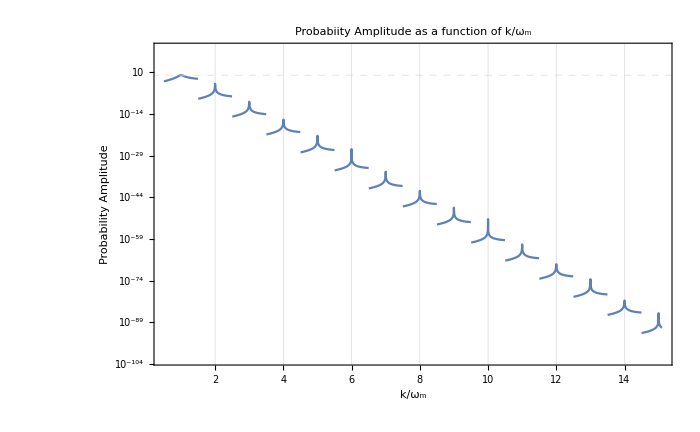

```mathematica
LogPlot[amplitude[1/k,0.1,Pi/4.01,Round[k]],{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"k/ω_m","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m"]
```

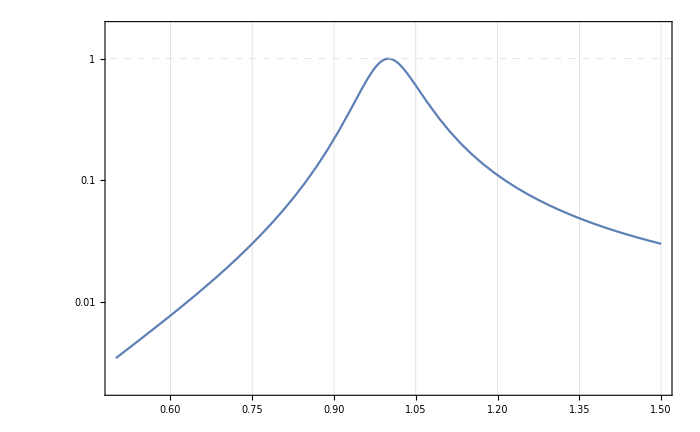

```mathematica
LogPlot[amplitude[1/k,0.1,Pi/7,Round[k]],{k,0.5,1.5},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed]]
```

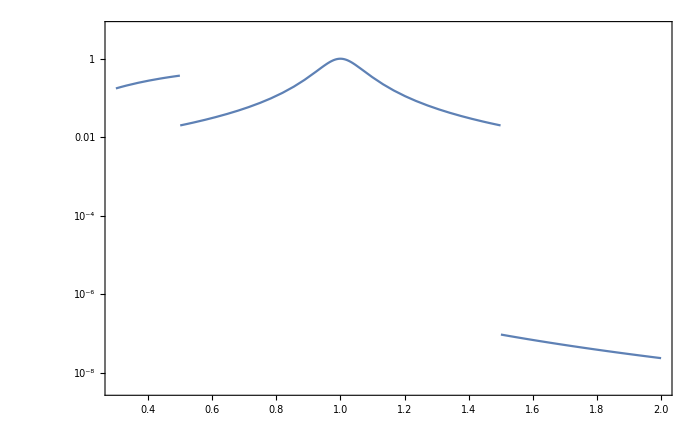

```mathematica
LogPlot[amplitude[k,0.1,Pi/5,Round[k]],{k,0.3,2},ImageSize->imgsize,Frame->True,PlotRange->Full]
```

```mathematica
Series[BesselJ[0,x],{x,0,3}]
```

1-x^2/4+O[x]^4

```mathematica
Limit[BesselJ[0,x]/x,x->0]
```

∞

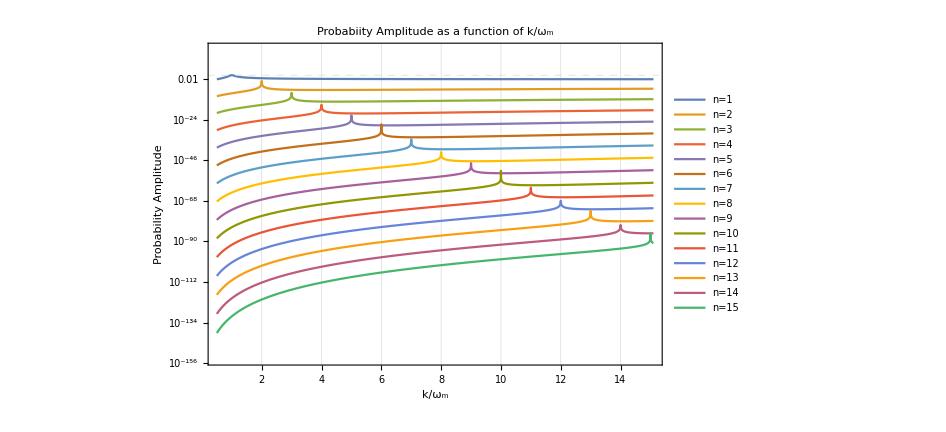

```mathematica
listFunctions=Table[amplitude[1/k,0.1,Pi/4.01,n],{n,1,15,1}];
listFunctionsLegends=Table["n="<>ToString@n,{n,1,15,1}];
LogPlot[listFunctions,{k,0.5,15.1},ImageSize->imgsize,Frame->True,PlotRange->Full,GridLines->{Automatic,{1}},GridLinesStyle->Directive[Thin,Dashed],FrameLabel->{"k/ω_m","Probability Amplitude"},PlotLabel->"Probabiity Amplitude as a function of k/ω_m",PlotLegends->listFunctionsLegends]
```

## 2-frequency system

```mathematica
ClearAll[k1,k2,x,phi1,phi2,psi1,psi2,lambdac,h,bFun,phase,a1,a2,h12,h12A,h12B]
```

Endpoint for NDSolve

```mathematica
endpoint=200
```

200

```mathematica
bFun[n1_,n2_,zk1_,zk2_,thetam_]:=Sin[2thetam]/4(-(-I)^(n1+n2))(2n1+1)/zk1 BesselJ[n1,zk1]BesselJ[n2,zk2]
phase[n1_,n2_,phi1_,phi2_]:=Exp[I(n1 phi1+n2 phi2)]
```

```mathematica
h1[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=a1 bFun[n1,n2p,zk1,zk2,thetam]phase[n1,n2p,phi1,phi2]Exp[I(n1 k1+n2p k2-1)x]
h2[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=a2 bFun[n2,n1p,zk2,zk1,thetam]phase[n1p,n2,phi1,phi2]Exp[I(n1p k1+n2 k2-1)x]
```

I have n1 =1, n2=1, n1p=Round[(n2 k2 - 1)/k1], n2p=Round[(n1 k1 - 1)/k2],

```mathematica
thetamV=Pi/5;
n1V=1;
n2V=1;
k1V=0.95;
k2V=1.03;
n1pV=Round[(n2V k2V-1)/k1V];
n2pV=Round[(n1V k1V-1)/k2V];
a1V=0.1;
a2V=0.2;
zk1V=a1V Cos[2thetamV]/k1V;
zk2V=a2V Cos[2thetamV]/k2V;
phi1V=0;
phi2V=0;
init={psi1[0],psi2[0]}=={1,0};
```

Include only the “most important” term in the series

```mathematica
h[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h2[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

```mathematica
(*zk=a Cos[2 thetam]/k*)
```

```mathematica
h12[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=h[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x]
(*h[1,1,Round[( k2-1)/k1],Round[(k1-1)/k2],k1,k2,a1,a2,a1 Cos[2thetam]/k1,a2 Cos[2thetam]/k2,phi1,phi2,thetam,x]*)
```

```mathematica
(*DSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12[k1,k2,a1,a2,phi1,phi2,thetam,x]},{Conjugate[h12[k1,k2,a1,a2,phi1,phi2,thetam,x]],0}}.{psi1[x],psi2[x]},{psi1,psi2},x]//FullSimplify*)
```

```mathematica
Re@h12[0.95,1.03,0.1,0.2,0,0,Pi/5,4] (*Test the function*)
Re@h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,4]
```

-0.00145473

-0.00145473

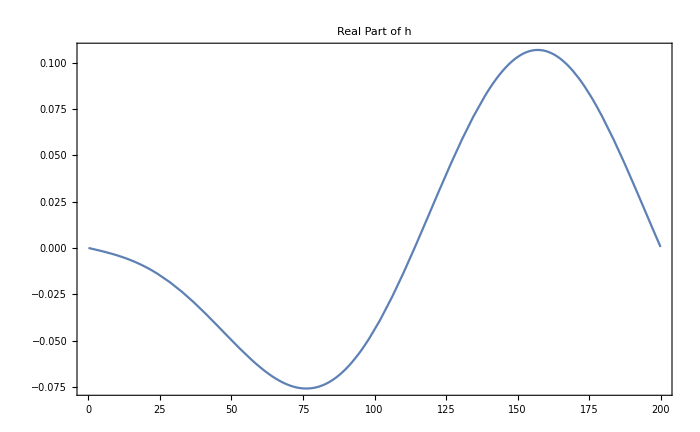

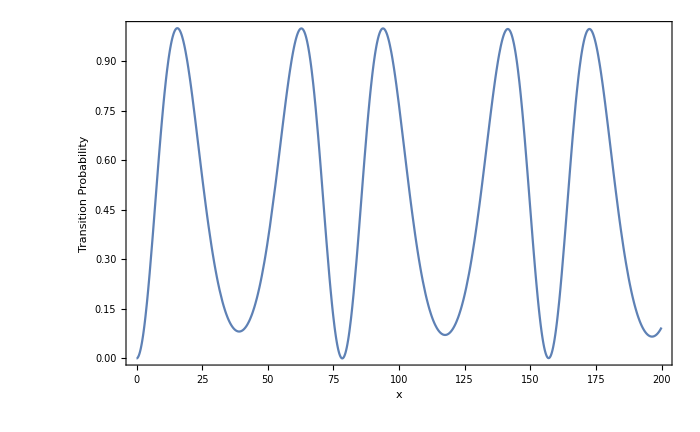

```mathematica
Plot[Re[h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

h12A[x_]:=h12[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];

solA=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12A[x]},{Conjugate[h12A[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

Plot[Evaluate[Abs[psi2[x]]^2/.solA],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```

#### Higher Order Series

Add only higher terms to see the interference of first term (interference from the first frequency resonance)

```mathematica
hB[n1_,n2_,n1p_,n2p_,k1_,k2_,a1_,a2_,zk1_,zk2_,phi1_,phi2_,thetam_,x_]:=h1[n1,n2,n1p,n2p,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+h1[n1,n2,n1p,n2p+1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]+
h1[n1,n2,n1p,n2p-1,k1,k2,a1,a2,zk1,zk2,phi1,phi2,thetam,x]
```

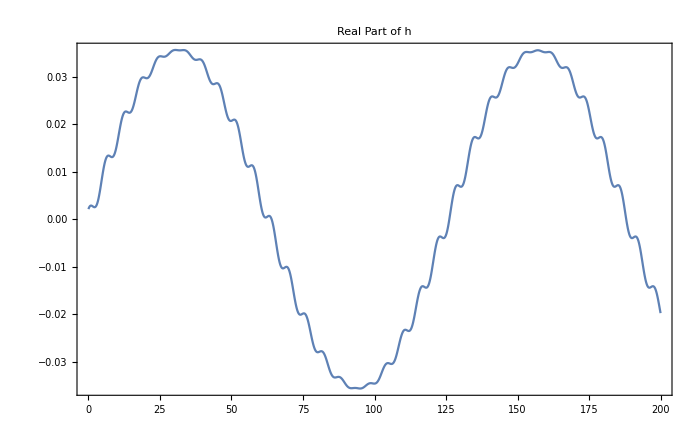

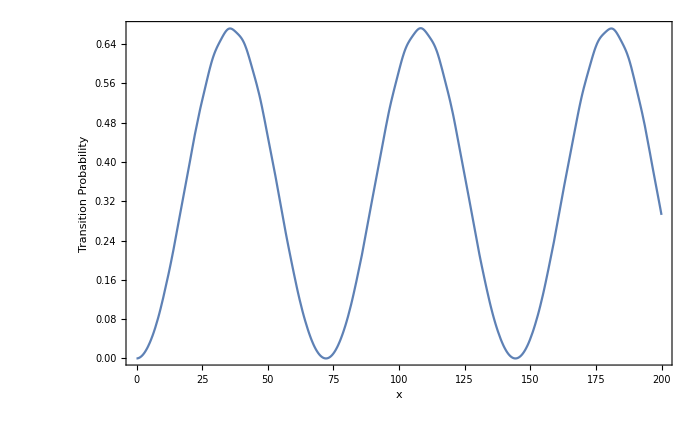

```mathematica
h12B[k1_,k2_,a1_,a2_,phi1_,phi2_,thetam_,x_]:=hB[n1V,n2V,n1pV,n2pV,k1,k2,a1,a2,zk1V,zk2V,phi1,phi2,thetam,x];

Plot[Re[h12B[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x]],{x,0,endpoint},Frame->True,ImageSize->imgsize,PlotLabel->"Real Part of h"]

h12B[x_]:=h12B[k1V,k2V,a1V,a2V,phi1V,phi2V,thetamV,x];
solB=NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,h12B[x]},{Conjugate[h12B[x]],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}];

Plot[Evaluate[Abs[psi2[x]]^2/.solB],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"}]
```